```mathematica
c=buildCC2D[{{1}}];
{numPT,pt,ct,kft,oit,olt,isE}=getNumParent[buildCC2D[{{1}}]];
numPT
pt
ct
kft
```

{{2,2,2,2},{1,1,1,1},{0}}

{{{1,4},{1,2},{2,3},{3,4}},{{1},{1},{1},{1}},{{}}}

{{{},{},{},{}},{{1,2},{2,3},{3,4},{4,1}},{{1,2,3,4}}}

{{False,False,False,False},{True,False,False,False},{True}}

```mathematica
{numPT2,pt2,ct2}=removeKilledParentIndex[numPT,pt,ct,kft,c];
numPT2
pt2
ct2
```

{{1,1,2,2},{0,0,0,0},{0}}

{{{4},{2},{2,3},{3,4}},{{},{},{},{}},{{}}}

{{{},{},{},{}},{{},{2,3},{3,4},{4,1}},{{}}}

```mathematica
{kft2,sp}=updateDisjoint[numPT2,kft,ct2,c]
```

22

24

{{{True,True,False,False},{True,True,False,True},{True}},2}

```mathematica
{numPT3,pt3,ct3}=removeKilledParentIndex[numPT2,pt2,ct2,kft2,c];
numPT3
pt3
ct3
```

{{0,0,1,1},{0,0,0,0},{0}}

{{{},{},{3},{3}},{{},{},{},{}},{{}}}

{{{},{},{},{}},{{},{},{3,4},{}},{{}}}

```mathematica
{kft3,sp}=updateDisjoint[numPT3,kft2,ct3,c]
```

23

{{{True,True,True,False},{True,True,True,True},{True}},1}

22

24

23

{{{0,0,0,0},{0,0,0,0},{0}},{{{},{},{},{}},{{},{},{},{}},{{}}},{{{},{},{},{}},{{},{},{},{}},{{}}},{{True,True,True,False},{True,True,True,True},{True}}}

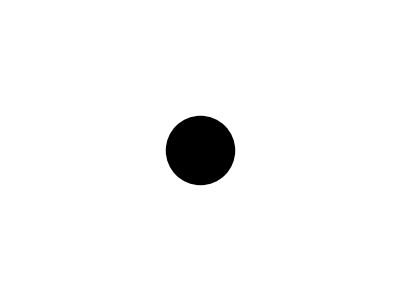

```mathematica
thinExhaustive[c]
```